# Frame Transform of Elastic Scattering (2D)

```mathematica
(* 1) given incident energy, scattering angle at CM frame, calculate the lab frame angle *)
ScatAngle
(* 2) given incident enegry, lab frame angle, calculate the CM frame angle *)

(* 3) given lab fram angle and CM frame angel, calculate the enegy. *)
```

```mathematica
c=299792458;
u = 931.494;
mp=938.27203;
mn=939.56536;
md=1875.612793; (* mass of deuteron *)
mT=2809.432; (* mass of Trilium*)
mHe4=3728.401;
mB11=10255.1;
mC12=11178;
mN13=12114.77;
mN21=19586.63;
mO13=12132.54;
mO14=13048.92;
mO21=19569.44;
mO22=20502.15;
mO23=21438.98;
mO24=22374.93;
mF23=21427.69;
mF24=22363.42;
massList={mp->"π",mn->"μ",mHe4->"α",mB11->"B11",mC12->"C12",mN13->"N13",mN21->"N21",mO13->"O13",mO14->"O14",mO21->"O21",mO22->"O22",mF23-> "F23"};
A[mass_]:=Floor[mass/u]
```

```mathematica
(* Tools *)
Angle[V_]:=If[V[[2]]==0 && V[[3]]==0,0,ArcTan[V[[2]],V[[3]]]]; 
(*Angle[V_]:= Arg[V[[2]]+ⅈ V[[3]]]*)
KE[V_,mass_]:=(V[[1]]-mass)/A[mass]
Momentum[V_]:=Norm[{V[[2]],V[[3]]}] (* MeV/c *)
Momentum2β[V_]:=Momentum[V]/V[[1]]
Momentum2γ[V_,mass_]:=V[[1]]/mass
Sp[mInc_,mTar_,T_,α_]:=Module[
{γ,β},
γ=(mInc+A[mInc]T)/mInc;
β=√(1-1/γ^2);
(  mInc+γ mTar)-γ(Pincident[mInc,mTar,T,α][[1]]+PTarget[mInc,mTar,T,α][[1]])+ γ β (Pincident[mInc,mTar,T,α][[2]]+PTarget[mInc,mTar,T,α][[2]])
]
```

```mathematica
SpLab[mInc_,mTar_,T_,α_]:=Module[
{γ,β},
γ=(mInc+A[mInc]T)/mInc;
β=√(1-1/γ^2);
( γ mInc +mTar)-(Pincident[mInc,mTar,T,α][[1]]+PTarget[mInc,mTar,T,α][[1]])
]
```

## Lab Frame

```mathematica
(* the effective operator of scattering *)
FullSimplify[Lz[-(√(2mInc T + T^2))/(mInc+mTar+T)].Rot[θ].Lz[(√(2mInc T + T^2))/(mInc+mTar+T)],mInc+mTar+T>0]
```

{{(m1+m2+T)/(√((m1+m2)^2+2 m2 T)),0,0,-(√(T (2 m1+T)))/(√((m1+m2)^2+2 m2 T))},{0,1,0,0},{0,0,1,0},{-(√(T (2 m1+T)))/(√((m1+m2)^2+2 m2 T)),0,0,(m1+m2+T)/(√((m1+m2)^2+2 m2 T))}}.Rot[θ].{{(m1+m2+T)/(√((m1+m2)^2+2 m2 T)),0,0,(√(T (2 m1+T)))/(√((m1+m2)^2+2 m2 T))},{0,1,0,0},{0,0,1,0},{(√(T (2 m1+T)))/(√((m1+m2)^2+2 m2 T)),0,0,(m1+m2+T)/(√((m1+m2)^2+2 m2 T))}}

```mathematica
(* incident particle *)
Pincident[mInc_,mTar_,T_,θ_]:={((mInc+mTar+A[mInc]T) (mInc (mInc+mTar)+mTar A[mInc]T)+mTar A[mInc]T (2 mInc+A[mInc]T) Cos[θ])/((mInc+mTar)^2+2 mTar A[mInc]T),(√(A[mInc]T (2 mInc+A[mInc]T)) (mInc (mInc+mTar)+mTar A[mInc]T+mTar (mInc+mTar+A[mInc]T) Cos[θ]))/((mInc+mTar)^2+2 mTar A[mInc] T),(mTar √(A[mInc]T (2 mInc+A[mInc]T)) Sin[θ])/(√((mInc+mTar)^2+2 mTar A[mInc] T))}
(* target particle *)
PTarget[mInc_,mTar_,T_,θ_]:={(mTar ((mInc+mTar+A[mInc]T)^2-A[mInc]T (2 mInc+T A[mInc]) Cos[θ]))/((mInc+mTar)^2+2 mTar A[mInc]T),(mTar √(A[mInc]T (2 mInc+A[mInc]T)) (mInc+mTar+A[mInc]T) (1-Cos[θ]))/((mInc+mTar)^2+2 mTar A[mInc]T),-(mTar √(A[mInc]T (2 mInc+A[mInc]T)) Sin[θ])/(√((mInc+mTar)^2+2 mTar A[mInc]T))}
Δθ[m1_,m2_,T_,θNN_]:=ArcCos[(Normalize[Pincident[m1,m2,T,θNN][[2;;3]]]).(Normalize[PTarget[m1,m2,T,θNN][[2;;3]]])]
```

```mathematica
(* if mInc=mTar *)
Remove[a,T];
FullSimplify[Pincident[a,a,T,θ],2a  +T>0]
Simplify[PTarget[a,a,T,θ],2a  +T>0]
```

{a+1/2 T (1+Cos[θ]) Floor[0.00107354 a],1/2 (1+Cos[θ]) √(T Floor[0.00107354 a] (2 a+T Floor[0.00107354 a])),(a √(T Floor[0.00107354 a] (2 a+T Floor[0.00107354 a])) Sin[θ])/(√(4 a^2+2 a T Floor[0.00107354 a]))}

{a+T Floor[0.00107354 a] Sin[θ/2]^2,√(T Floor[0.00107354 a] (2 a+T Floor[0.00107354 a])) Sin[θ/2]^2,-(a √(T Floor[0.00107354 a] (2 a+T Floor[0.00107354 a])) Sin[θ])/(√(4 a^2+2 a T Floor[0.00107354 a]))}

```mathematica
(* Simple momentum plot *)
Manipulate[
Show[
ParametricPlot[{
Pincident[mInc,mTar,T,θ °][[2;;3]],
PTarget[mInc,mTar,T,θ °][[2;;3]]
},{θ,0,360},PlotStyle->{Red,Blue},ImageSize->600],
Graphics[
{{Black,Arrow[{{-√(2mInc T+T^2),0},{0,0}}]},
{Red,Arrow[{{0,0},Pincident[mInc,mTar,T,α °][[2;;3]]}]},
{Blue,Arrow[{{0,0},PTarget[mInc,mTar,T,α °][[2;;3]]}]},
{Red,Text[Round[{Momentum[Pincident[mInc,mTar,T,α °]],Angle[Pincident[mInc,mTar,T,α °]] 180/π},0.1],{Pincident[mInc,mTar,T,α °][[2]],Pincident[mInc,mTar,T,α °][[3]]}{0.9,0.6}]},
{Blue,Text[Round[{Momentum[PTarget[mInc,mTar,T,α °]],Angle[PTarget[mInc,mTar,T,α °]] 180/π},0.1],{PTarget[mInc,mTar,T,α °][[2]],PTarget[mInc,mTar,T,α °][[3]]}{0.9,0.6}]},
Text[Style["T="<>ToString[T],16],{-(√(mInc T))/(√2), 0.5 (√(mInc T))/(√2)}],
Gray,Line[{{0,0},1000{Cos[70 °],Sin[70 °]}}],
Line[{{0,0},1000{Cos[20 °],Sin[20 °]}}],
Line[{{0,0},1000{Cos[70 °],-Sin[70 °]}}],
Line[{{0,0},1000{Cos[20 °],-Sin[20 °]}}]
}
]
],
{{α,45},0,360},{{mInc,mO14},massList},{{mTar,mC12},massList},{T,260,300}]
```

```mathematica
Manipulate[
GraphicsGrid[{{
Plot[KE[Pincident[mInc,mTar,T,θ °],mInc]-KE[PTarget[mInc,mTar,T,θ °],mTar],{θ,40,140},PlotStyle->{Red,RGBColor[0,0.6,0], Blue},AspectRatio->0.8,GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["θ_NN[deg]",14],Style["ΔKE[MeV]",14]}],
Plot[Δθ[mInc,mTar,T,θ °]*180/π,{θ,0,180},PlotStyle->{Blue},PlotRange->All,GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted], AspectRatio->0.8,Frame->True,FrameLabel->{Style["θ_NN[deg]",14],Style["Δθ[deg]",14]}],
Plot[{KE[Pincident[mInc,mTar,T,θ °],mInc],KE[PTarget[mInc,mTar,T,θ °],mTar],KE[Pincident[mInc,mTar,T,θ °],mInc]+KE[PTarget[mInc,mTar,T,θ °],mTar]}
,{θ,0,180},PlotStyle->{Red, Blue,Green},GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["θ_NN[deg]",14],Style["KE[MeV]",14]},AspectRatio->0.8,
Epilog->{Red, Text[ToString[mInc]<>"(Incident)",{140, 160}], Blue, Text[ToString[mTar]<>"(Target)",{140, 90}]}],
Plot[{Abs[Angle[Pincident[mInc,mTar,T,θ °]]] 180/π,Abs[Angle[PTarget[mInc,mTar,T,θ °]]] 180/π},{θ,0,180},PlotStyle->{Red,Blue},PlotRange->All,GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted], AspectRatio->0.8,Frame->True,FrameLabel->{Style["θ_NN[deg]",14],Style["θ[deg]",14]}]
},
{ParametricPlot[{
{Abs[Angle[Pincident[mInc,mTar,T,α ]]] 180/π,Δθ[mInc,mTar,T,α]*180/π},
{Abs[Angle[PTarget[mInc,mTar,T,α ]]] 180/π,Δθ[mInc,mTar,T,α]*180/π}
},{α,0.001,π-0.001},PlotRange->{{20,70},{0,All}},GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["|θ|[deg]",14],Style["Δθ[deg]",14]},AspectRatio->0.8,PlotStyle->{Red, Blue}],
ParametricPlot[{
{Abs[Angle[Pincident[mInc,mTar,T,α ]]] 180/π,KE[Pincident[mInc,mTar,T,α],mInc]},
{Abs[Angle[PTarget[mInc,mTar,T,α ]]] 180/π,KE[PTarget[mInc,mTar,T,α],mTar]}
},{α,0,π},PlotRange->{{20,70},{0,All}},GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["|θ|[deg]",14],Style["KE[MeV/u]",14]},AspectRatio->0.8,PlotStyle->{Red, Blue}],
ParametricPlot[{Abs[Angle[Pincident[mInc,mTar,T,α ]]] 180/π,Abs[Angle[PTarget[mInc,mTar,T,α]]] 180/π},{α,0,π},AspectRatio->0.8,PlotRange->All,GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["|θ_inc|[deg]",14],Style["|θ_Target|[deg]",14]}],
ParametricPlot[{KE[Pincident[mInc,mTar,T,α ],mInc],KE[PTarget[mInc,mTar,T,α],mTar]},{α,0,π},GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["KE_inc[MeV]",14],Style["KE_Target[MeV]",14]},AspectRatio->0.8]

},
{ParametricPlot[{Δθ[mInc,mTar,T,α]*180/π,KE[Pincident[mInc,mTar,T,α ],mInc]+KE[PTarget[mInc,mTar,260,α],mTar]},{α,0.001,π},GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["Δθ[deg]",14],Style["ΣKE[MeV]",14]},AspectRatio->0.8],
ParametricPlot[{Δθ[mInc,mTar,T,α]*180/π,KE[Pincident[mInc,mTar,T,α ],mInc]-KE[PTarget[mInc,mTar,260,α],mTar]},{α,0.001,π},GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["Δθ[deg]",14],Style["ΔKE[MeV]",14]},AspectRatio->0.8],
ParametricPlot[{KE[Pincident[mInc,mTar,T,α ],mInc]-KE[PTarget[mInc,mTar,260,α],mTar],KE[Pincident[mInc,mTar,T,α ],mInc]+KE[PTarget[mInc,mTar,260,α],mTar]},{α,0.001,π},GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["ΔKE[MeV]",14],Style["ΣKE[MeV]",14]},AspectRatio->0.8]
}},ImageSize->1000,PlotLabel->"K.E_inc="<>ToString[T]<>"MeV/u = "<>ToString[T A[mInc]]<>"MeV"], 
{{mInc,mO14},massList},{{mTar,mC12},massList},{T,260,360}]
```

```mathematica
(* Numerical *)
Manipulate[TableForm[
{{"","|θ|", "KE[MeV/u]", "k[MeV/c]"},
{"mTar",Abs[Angle[Pincident[mInc,mTar,T,α  °]]] 180/π,KE[Pincident[mInc,mTar,T,α °],mInc],Momentum[Pincident[mInc,mTar,T,α °]]},
{"mInc",Abs[Angle[PTarget[mInc,mTar,T,α  °]]] 180/π,KE[PTarget[mInc,mTar,T,α °],mTar],Momentum[PTarget[mInc,mTar,T,α °]]},
{"Σ KE",KE[Pincident[mInc,mTar,T,α °],mInc]+KE[PTarget[mInc,mTar,T,α °],mTar], "ΔKE",KE[Pincident[mInc,mTar,T,α °],mInc]-KE[PTarget[mInc,mTar,T,α °],mTar]},
{"Δθ",Δθ[mInc,mTar,T,α °]*180/π,"Sp", Sp[mInc,mTar,T,α]}
}],{α,0,180},{{mInc,mp},massList},{{mTar,mC12},massList},{T,260,300}]
```

```mathematica
(* for non-relativistic case *)
PIg[mInc_,mTar_,T_,θ_]:=1/(mInc+mTar)√(2mInc A[mInc]T){0, mInc+mTar Cos[θ],mTar Sin[θ]}
PTg[mInc_,mTar_,T_,θ_]:=1/(mInc+mTar)√(2mInc A[mInc]T){0, mTar-mTar Cos[θ],-mTar Sin[θ]}
```

```mathematica
(* momentum plot - Compare *)
Manipulate[
Show[
ParametricPlot[{
PIg[mInc,mTar,T,θ °][[2;;3]],
PTg[mInc,mTar,T,θ °][[2;;3]],
Pincident[mInc,mTar,T,θ °][[2;;3]],
PTarget[mInc,mTar,T,θ °][[2;;3]]
},{θ,0,360},PlotStyle->{ Blue,Red, Purple,Orange},ImageSize->600],
Graphics[
{
{Blue,Arrow[{{0,0},PIg[mInc,mTar,T,α °][[2;;3]]}]},
{Red,Arrow[{{0,0},PTg[mInc,mTar,T,α °][[2;;3]]}]},
{Green,Arrow[{PTg[mInc,mTar,T,α °][[2;;3]],PIg[mInc,mTar,T,α °][[2;;3]]}]},
{Purple,Arrow[{{0,0},Pincident[mInc,mTar,T,α °][[2;;3]]}]},
{Orange,Arrow[{{0,0},PTarget[mInc,mTar,T,α °][[2;;3]]}]},
{Gray,Arrow[{PTarget[mInc,mTar,T,α °][[2;;3]],Pincident[mInc,mTar,T,α °][[2;;3]]}]},
{Blue,Text[Round[{Norm[PIg[mInc,mTar,T,α °]],Angle[PIg[mInc,mTar,T,α °]] 180/π},0.1],PIg[mInc,mTar,T,α °][[2;;3]]{0.9,0.8}]},
{Red,Text[Round[{Norm[PTg[mInc,mTar,T,α °]],Angle[PTg[mInc,mTar,T,α °]] 180/π},0.1],PTg[mInc,mTar,T,α °][[2;;3]]{0.9,0.8}]},
{Purple,Text[Round[{Momentum[Pincident[mInc,mTar,T,α °]],Angle[Pincident[mInc,mTar,T,α °]] 180/π},0.1],{Pincident[mInc,mTar,T,α °][[2]],Pincident[mInc,mTar,T,α °][[3]]}{0.9,0.6}]},
{Orange,Text[Round[{Momentum[PTarget[mInc,mTar,T,α °]],Angle[PTarget[mInc,mTar,T,α °]] 180/π},0.1],{PTarget[mInc,mTar,T,α °][[2]],PTarget[mInc,mTar,T,α °][[3]]}{0.9,0.6}]},
Text[α,{(√(mInc T))/(√2),0.1(√(mInc T))/(√2)}],
Text[Style["T="<>ToString[T]<>"MeV/u",16],{(√(mInc T))/(√2), 0.5 (√(mInc T))/(√2)}]}
]
],
{{α,45},0,360},{{T,260},0,6000},{{mInc,mp},massList},{{mTar,mC12},massList}]
```

## Transform

```mathematica
(* 4 vectors *)(* operator applied from right *)
Pm[KE_,mass_]:={mass+KE,0,√(2mass KE+KE^2)}
Ps[mass_]:={mass,0,0}
Pc[p1_,p2_]:=(p1+p2)/2
Lβ[p_]:=(√(p[[2]]^2+p[[3]]^2))/p[[1]]
Lz[β_]:={{1/(√(1-β^2)),0,β/(√(1-β^2))},{0,1,0},{β/(√(1-β^2)),0,1/(√(1-β^2))}};
Rot[θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}}
```

```mathematica
ScatAngle[energy_,θCM_,massInc_,massTar_]:={
Pd=Pm[energy,massInc];
Pp=Ps[massTar];
Pdc=Pd.Lz[-Lβ[Pc[Pd,Pp]]];
Ppc=Pp.Lz[-Lβ[Pc[Pd,Pp]]];
Kdc=Pdc.Rot[θCM °];
Kpc=Ppc.Rot[θCM °];
Kd=Kdc.Lz[Lβ[Pc[Pd,Pp]]];
Kp=Kpc.Lz[Lβ[Pc[Pd,Pp]]];
Angle[Kd],
Angle[Kp],
KE[Kd,md],
KE[Kp,mp],
{Kd[[3]],Kd[[2]]},
{Kp[[3]],Kp[[2]]}
}
```

```mathematica
Manipulate[ScatAngle[294*2,θNN,md,mp][[5]];
TableForm[
{Pp,
Pd,
Pp.Lz[-Lβ[Pd]],
Pd.Lz[-Lβ[Pd]],
Pc[Pd,Pp],
Lβ[Pc[Pd,Pp]],
Pc[Pd,Pp].Lz[-Lβ[Pc[Pd,Pp]]],
Ppc,
Pdc,
Kpc,
Kdc,
Kp,
Kd,
{Angle[Kp],Angle[Kd],Kp[[1]]-mp,Kd[[1]]-md},
Pp.Lz[-Lβ[Pd]][[1]]-mp
}]
,{{θNN,77},0,180}]
```

```mathematica
Manipulate[
Show[
ListPlot[{Table[ScatAngle[294*2,θCM ,md,mp][[5]],{θCM,0,360,1}],
Table[ScatAngle[294*2,θCM ,md,mp][[6]],{θCM,0,360,1}]
},AspectRatio->Automatic,Joined->True,PlotStyle->{Blue,Red}],
Graphics[
{
{Blue,Arrow[{{0,0},ScatAngle[294*2,α,md,mp][[5]]}]},
{Red,Arrow[{{0,0},ScatAngle[294*2,α,md,mp][[6]]}]},
{Green,Arrow[{ScatAngle[294*2,α,md,mp][[6]],ScatAngle[294*2,α,md,mp][[5]]}]}
}]
],
{α,0,360}]
```

```mathematica
(* by using analytic function *)
Manipulate[
Show[
ParametricPlot[{{Pincident[md,mp,294*2,θ °][[2]],Pincident[md,mp,294*2,θ °][[3]]},{PTarget[md,mp,294*2,θ °][[2]],PTarget[md,mp,294*2,θ °][[3]]}},{θ,0,360},AspectRatio->Automatic,PlotStyle->{ Blue, Red}],
Graphics[
{
{Blue,Arrow[{{0,0},ScatAngle[294*2,α,md,mp][[5]]}]},
{Red,Arrow[{{0,0},ScatAngle[294*2,α,md,mp][[6]]}]},
{Green,Arrow[{ScatAngle[294*2,α,md,mp][[6]],ScatAngle[294*2,α,md,mp][[5]]}]}
}]
],
{α,0,360}]
```

```mathematica
NumberForm[{θCM,
ScatAngle[294*2,θCM,md,mp][[1]],
ScatAngle[294*2,θCM,md,mp][[2]],
ScatAngle[294*2,θCM,md,mp][[3]],
ScatAngle[294*2,θCM,md,mp][[4]]}/.θCM->152.9,5]
```

{152.9,0.4058,-0.20966,86.4,501.6}

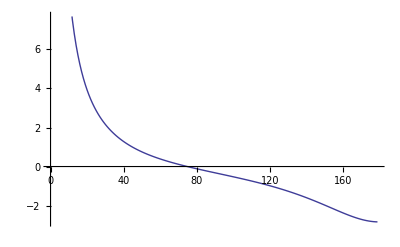

```mathematica
(* TOF difference *)
ListPlot[Table[{θCM,ScatAngle[294*2,θCM,md,mp];1/Lβ[Kp]-1/Lβ[Kd]},{θCM,1,179,1}],Joined->True]
```

```mathematica
(* Qusi-Free Scatterin of Proton *)
Manipulate[
Show[
ListPlot[{Table[ScatAngle[294,θCM ,mp,mp][[5]],{θCM,0,360,1}],
Table[ScatAngle[294,θCM ,mp,mp][[6]],{θCM,0,360,1}]
},AspectRatio->1,Joined->True],
Graphics[
{{Blue,Arrow[{{0,0},ScatAngle[294,α,mp,mp][[5]]}]},
{Red,Arrow[{{0,0},ScatAngle[294,α,mp,mp][[6]]}]},
{Green,Arrow[{ScatAngle[294,α,mp,mp][[6]],ScatAngle[294,α,mp,mp][[5]]}]}
}]
],
{α,0,360}]
```

```mathematica
NumberForm[{θCM,ScatAngle[294,θCM,mp,mp][[1]],ScatAngle[294,θCM,mp,mp][[2]],ScatAngle[294,θCM,mp,mp][[3]],ScatAngle[294,θCM,mp,mp][[4]]}/.θCM->77,7]
```

{77,36.48684,-49.45366,-757.273,113.9322}

```mathematica
(* TOF *)
NumberForm[
ScatAngle[294,θCM,mp,mp];
{θCM,1/Lβ[Kp],1/Lβ[Kd]}/.θCM->77,7]
```

{77,2.209522,1.837721}

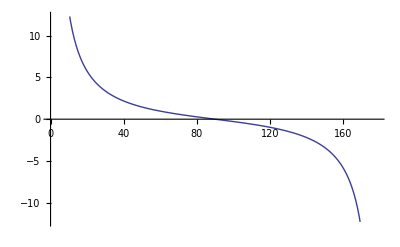

```mathematica
ListPlot[Table[{θCM,ScatAngle[294,θCM,mp,mp];1/Lβ[Kp]-1/Lβ[Kd]},{θCM,1,179,1}],Joined->True]
```